```mathematica
PlotInfluenceFunctionApprox[score_,numC_]:=Block[{},
k = numC;

(*Bayes Decision Rule Regions; Ri=(a_i,b_i)*)
fraction[c_,ϵ_] := If [(1/c-ϵ/(c-1))== 0, Infinity,(1/c+ϵ)/(1/c-ϵ/(c-1)) ];

(* 
a_i =   -∞                                                                               if i=1
    1/(2λ)*(2*σ*Log[(1/k+ϵ)/(1/k-ϵ/(k-1))]+λ^2)                                     if i=2
    max{ λ/2*(2i-3) , 1/(2(i-1)λ)*(2*σ*Log[(1/k+ϵ)/(1/k-ϵ/(k-1))]+(i-1)^2λ^2)}     otherwise	 
*)
A[ϵ_?NumericQ,σ_,λ_?NumericQ,i_]:=Block[{maxVal=+Infinity},
If[i≠ 1,
If[i==2,maxVal = 1/(2λ)*(2*σ^2*Log[fraction[k,ϵ]]+ λ^2),
maxVal = Max[1/(2(i-1)λ)*(2*σ^2*Log[fraction[k,ϵ]]+ (i-1)^2*λ^2),(2i-3)*λ/2]],maxVal=-Infinity];maxVal
];

(*
b_i =    ∞                                               if i=k
    1/(2λ)*(2*σ*Log[(1/k+ϵ)/(1/k-ϵ/(k-1))]+λ^2)     if i=1
    λ/2*(2i-3)                                      otherwise	 
*)
B[ϵ_?NumericQ,σ_,λ_?NumericQ,i_]:=Block[{minVal= -Infinity},
If[i≠ k,
If[i==1,minVal = 1/(2λ)*(2*σ^2*Log[fraction[k,ϵ]]+ λ^2),
minVal =(2i-1)*λ/2],minVal=Infinity];minVal
];

m::ps="The score `1` is not supported";
priors[c_,e_] := If[c==1,((1/k)+e),(1/k-e/(k-1))];

Clear[m];
m[ λ_?NumericQ,ϵ_?NumericQ,k_]:=
Switch[score,

"REC",(*Recall_i: (F_i(b_i)-F_i(a_i))*)
(*Class 1*)i=1;
scoreString = "Recall for class 1";
Boole[B[ϵ,1,λ,i]> A[ϵ,1,λ,i]]*(CDF[NormalDistribution[(i-1)λ,1],B[ϵ,1,λ,i]]-CDF[NormalDistribution[(i-1)λ,1],A[ϵ,1,λ,i]]),

"AMN",(*A-mean: (1/K)*Sum_{i=1}^K (F_i(b_i)- F_i(a_i))*)
scoreString = "Arithmetic Mean among the recalls";
(Sum[Boole[B[ϵ,1,λ,c]> A[ϵ,1,λ,c]]*(CDF[NormalDistribution[(c-1)λ,1],B[ϵ,1,λ,c]]-CDF[NormalDistribution[(c-1)λ,1],A[ϵ,1,λ,c]]),{c,1,k}])/k,

"ACC",(*Accuracy: Sum_{i=1}^K η_i(F_i(b_i)- F_i(a_i))*)
scoreString = "classfication Accuracy";
Sum[Boole[B[ϵ,1,λ,c]> A[ϵ,1,λ,c]]*priors[c,ϵ]*(CDF[NormalDistribution[(c-1)λ,1],B[ϵ,1,λ,c]]-CDF[NormalDistribution[(c-1)λ,1],A[ϵ,1,λ,c]]),{c,1,k}],

"GMN",(*G-mean: Sqrt[Prod_{i=1}^K (F_i(b_i)- F_i(a_i)),k]*)
scoreString = "Geometric Mean among the recalls";
(Product[Boole[B[ϵ,1,λ,c]> A[ϵ,1,λ,c]]*(CDF[NormalDistribution[(c-1)λ,1],B[ϵ,1,λ,c]]-CDF[NormalDistribution[(c-1)λ,1],A[ϵ,1,λ,c]]),{c,1,k}])^(1/k),

"HMN",(*H-mean: (K)*(Sum_{i=1}^K 1/(F_i(b_i)- F_i(a_i)))^(-1)*)
scoreString = "Harmonic Mean among the recalls";
If[Product[Boole[B[ϵ,1,λ,c]> A[ϵ,1,λ,c]],{c,1,k}]==0,0,k*(Sum[1/(CDF[NormalDistribution[(c-1)λ,1],B[ϵ,1,λ,c]]-CDF[NormalDistribution[(c-1)λ,1],A[ϵ,1,λ,c]]),{c,1,k}])^(-1)],

"MAX",(*Max: max[(F_i(b_i)- F_i(a_i))]*)
scoreString = "Maximum Recall";
Max[Table[Boole[B[ϵ,1,λ,c]> A[ϵ,1,λ,c]]*(CDF[NormalDistribution[(c-1)λ,1],B[ϵ,1,λ,c]]-CDF[NormalDistribution[(c-1)λ,1],A[ϵ,1,λ,c]]),{c,1,k}]],

"MIN",(*Min: min(F_i(b_i)- F_i(a_i))]*)
scoreString = "Minimum Recall";Min[Table[Boole[B[ϵ,1,λ,c]> A[ϵ,1,λ,c]]*(CDF[NormalDistribution[(c-1)λ,1],B[ϵ,1,λ,c]]-CDF[NormalDistribution[(c-1)λ,1],A[ϵ,1,λ,c]]),{c,1,k}]],

_,Message[m::ps,score];Exit[]];

(*Computation of the influence function as expressed in eq. 10 of the manuscript*)
InfluenceF[ϵ_?NumericQ,k_]:= NIntegrate[m[λ,0,k]-m[λ,ϵ,k],{λ,0.01,10},AccuracyGoal->3];

(*Plotting the function for the whole domain of ϵ*)
Print[
Style["Influence Function for the ",18,Black],
Style[scoreString,18,Black, Bold],Style["assesing the Bayes Decision Rule in a ",18,Black],
Style[k,18,Black],
Style["-class problem",18,Black]];
Print[Plot[InfluenceF[ϵ,k],{ϵ,-1/k+0.0001,1-1/k-0.0001},AxesLabel->Automatic, PlotStyle->Thick,Filling->Axis,
PlotTheme-> "Detailed",
PlotRange-> {-4,4},
Axes -> True,
BaseStyle->{FontFamily->"Times",FontSize->20},
Ticks->{{0,-1/k,0,1-1/k},{-3,0,3}},
ImageSize->600]];
];
```

```mathematica
PlotScoreCompetitivenessBounds[numC_]:=Block[{},
k = numC;
(*Bounds, eq. 17 and 18 of the manuscript*)
SSup[p_]:= ((1/k)*(k-1+1/k^p))^(1/p);
SInf[p_] := 1/k;

(*Plotting the function for p in [-50,50]*)
Print[
Style["Comparison to the uniformly random classifier in a ",18,Black],
Style[k,18,Black],
Style["-class problem",18,Black]];
p1=Plot[{SSup[p],SInf[p]},{p,-50,50},Filling->{{(1)  -> 1},{(2)  -> 0}}, AxesLabel->{"p","Score"}, PlotRange->{0,1},Epilog->{Style[Text["SUPERIOR",{-25,0.75}],14],Style[Text["INFERIOR",{0,0.05}],14],Style[Text["INDETERMINATE",{25,0.75}],14]},PlotTheme->"Detailed", Axes -> True,ImageSize->600];Print[p1]
];
```

Comparison to the uniformly random classifier in a 2-class problem

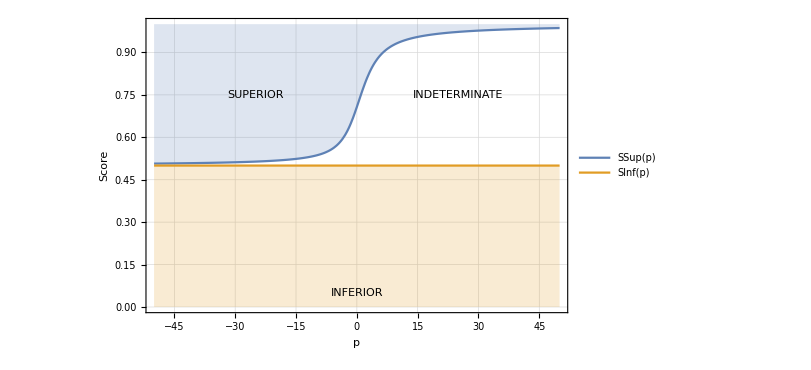

```mathematica
PlotScoreCompetitivenessBounds[2]
```

Influence Function for the Maximum Recallassesing the Bayes Decision Rule in a 2-class problem

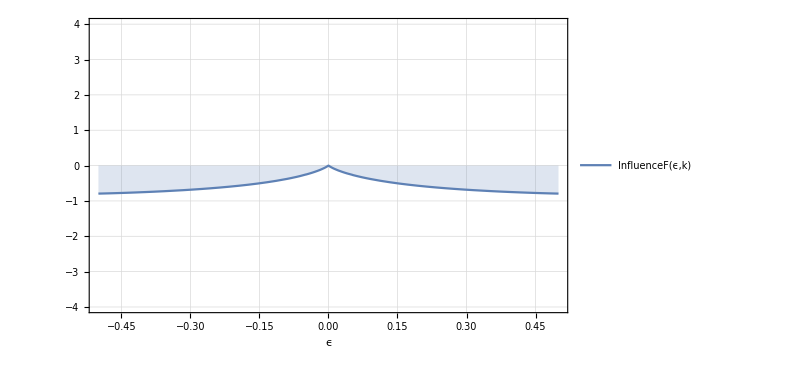

```mathematica
PlotInfluenceFunctionApprox["MAX",2]
```